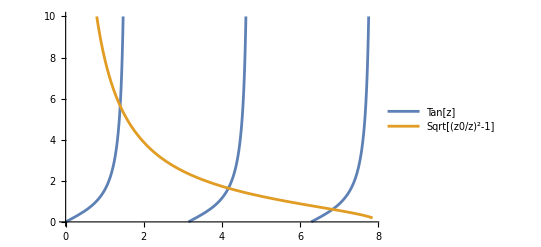

```mathematica
(*Even parity*)
X1[z_]:=Tan[z];
X2[z_]:= Sqrt[(z0/z)^2-1];
Block[{z0=8},Plot[{X1[z],X2[z]},{z,0,(5 Pi)/2},PlotRange->{0,10},PlotLegends->{"Tan[z]","Sqrt[(z0/z)^2-1]"},GridLines->{Table[n,{n,0,5 Pi/2,Pi/2}],None},GridLinesStyle->Directive[Dashed,Black]]]
```

```mathematica
(*Odd parity*)
X3[z_]:=-Cot[z];
```

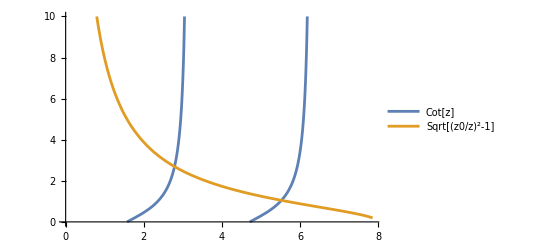

```mathematica
Block[{z0=8},Plot[{X3[z],X2[z]},{z,0,(5 Pi)/2},PlotRange->{0,10},PlotLegends->{"Cot[z]","Sqrt[(z0/z)^2-1]"},GridLines->{Table[n,{n,0,5 Pi/2,Pi/2}],None},GridLinesStyle->Directive[Dashed,Black]]]
```

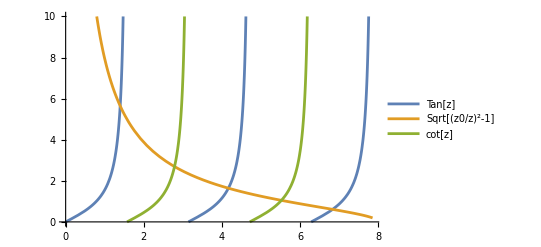

```mathematica
Block[{z0=8},Plot[{X1[z],X2[z],X3[z]},{z,0,(5 Pi)/2},PlotRange->{0,10},PlotLegends->{"Tan[z]","Sqrt[(z0/z)^2-1]","cot[z]"},GridLines->{Table[n,{n,0,5 Pi/2,Pi/2}],None},GridLinesStyle->Directive[Dashed,Black]]]
```